## Multilayer-layer perceptron

### 1. Introduction: Training a multilayer-layer perceptron

```mathematica
CellPrint[TextCell["This algorithm encodes a general multilayer perceptron with variable number of layers, inputs and outputs.","Text",CellFrame->True,CellMargins->{{65,400},{10,10}}]]
```

This algorithm encodes a general multilayer perceptron with variable number of layers, inputs and outputs.

### 2. Set parameters

```mathematica
CellPrint[TextCell["Parameters go here if any.  Define also the important 'stateSizeList' list, which gives the number of nodes in each layer, starting with the input layer, moving onto the hidden layers (if any) and ending with the output layer.","Text",CellFrame->True,CellMargins->{{65,400},{10,10}}]]
```

Parameters here if any.

```mathematica
stateSizeList={4,5,1};
```

### 3. Randomize weight matrix

```mathematica
CellPrint[TextCell["Randomly generate a weight matrix 'w' with Gaussian-distributed values.","Text",CellFrame->True,CellMargins->{{65,400},{10,10}}]]
```

Randomly generate a weight matrix 'w' with Gaussian-distributed values.  Note that a “perfect weight” list for the XOR function is given below but commented out.

```mathematica
w={};
For[i=1,i≤(Length[stateSizeList]-1),i++,
q=RandomVariate[NormalDistribution[],{stateSizeList[[i+1]],stateSizeList[[i]]+1}];
(*Print["q generated ",q];*)
w=Append[w,q];
];
w
(*w={{{-3.5,7,7},{10,-7,-7}},{{-10,7,7}}}*)
```

### 3. Load training data

```mathematica
CellPrint[TextCell["1st block is for importing inputs and outputs as separate files.  2nd block imports it as one file, so user must define which columns are inputs and outputs to separate them out.","Text",CellFrame->True,CellMargins->{{65,400},{10,10}}]]
```

Imports training input as one file, so user must define which columns are inputs and outputs to separate them out.  In the default case, we use the state sizes defined in the list above.  A header and first column are discarded.  For now, the entire training set is used but may be separated into two parts for training and testing independently.

```mathematica
SetDirectory["/Users/williamchen/ScienceProjects/MLPerceptron/mathematica"];

tempSet = Import["sp500-data.txt","Table"];
tempSet=Take[tempSet,{2,-1},{2,-1} ];
altTrainingInput =Take[tempSet,All,{1,-(1+stateSizeList[[-1]])} ];
altTrainingOutput=Take[tempSet,All,{-(stateSizeList[[-1]]),-1}];
altTrainingSet=Thread[{altTrainingInput,altTrainingOutput}];
```

### 5. Set up the sigmoid function and its derivative

```mathematica
CellPrint[TextCell["Define the sigmoid functions and derivative.  Set the learning rate.","Text",CellFrame->True,CellMargins->{{65,400},{10,10}}]]
```

Define the sigmoid functions and derivative.  Set the learning rate.

```mathematica
sigmoid[x_]:=2/(1+Exp[-x])-1;
dsigmoid[x_]:=(2 ⅇ^-x)/((1+ⅇ^-x)^2);
sigmoid2dsigmoid[x_]:=1/2*(1+x)(1-x);
eta=0.01;
```

### 8. Set up the output function as a function of inputs and the given weight vector. Save the inner states during calculation for back propagation.

```mathematica
CellPrint[TextCell["This computes the neural network output for a given input.  First the neural network weight matrix w is populated with random entries.  Then the output function is defined.  The output function passes the input through successive layers of the network, saving the state at each time.","Text",CellFrame->True,CellMargins->{{65,400},{10,10}}]]
```

This computes the neural network output for a given input.  1.  First the neural network weight matrix w is populated with random entries.  2.  Then the output function is defined.  3.  The output function passes the input through successive layers of the network, saving the state at each time.

```mathematica
nnStates[input_,w_]:=Module[{currentStates={},currentState,tempoutput},
For[currentStates=Append[currentStates,input];
i=2,i≤(Length[stateSizeList]),i++,
tempoutput = w[[i-1]].Prepend[currentStates[[i-1]],1];
currentState=Map[sigmoid[#]&,tempoutput];
currentStates=Append[currentStates,currentState];
];
currentStates
]
nnOutput[input_,w_]:=Module[{},
Last[nnStates[input,w]]
]
```

### 9-1. Back-propagation - Picking a single input output pair and perform gradient descent

```mathematica
CellPrint[TextCell["Pick a training vector.  Start with the last level.","Text",CellFrame->True,CellMargins->{{65,400},{10,10}}]]
```

Feed this module a training input vector, the associated target output vector, and it will return the list of modifications to all w matrices.  Run this module inside a back propagation loop.

```mathematica
backPropagate[input_, targetOutput_,w_]:=Module[{error={},dwlist={},currError=0,currentStates={},currOutput={},currW,currentState={},nextError},
currentStates=nnStates[input,w];
currOutput = Last[currentStates];
currError = -1*(currOutput - targetOutput)*Map[sigmoid2dsigmoid[#]&,currOutput];
error=Prepend[error ,currError];
For[i=Length[stateSizeList]-1,i>=1,i--,
currW = w[[i]];
currentState = currentStates[[i]];
nextError = (Transpose[currW[[All,2;;-1]]].currError) * Map[sigmoid2dsigmoid[#]&,currentState];
error=Prepend[error,nextError];
currError=nextError;
];
For[i=Length[stateSizeList]-1,i≥1,i--,
dw = KroneckerProduct[error[[i+1]],Prepend[currentStates[[i]],1] ];
dwlist = Prepend[dwlist,dw];
];
dwlist
]
```

### 9-2. Back - propagation - Use full objective function

```mathematica
backPropagate2[altTrainingInput_, altTrainingOutput_,w_]:=Module[{i,tempdw,dwlist={}},
For[i=1,i≤Length[altTrainingInput],i++,
tempdw=backPropagate[altTrainingInput[[i]],altTrainingOutput[[i]],w];
dwlist=Append[dwlist,tempdw];
];
Total[dwlist]
]
```

### 10. Scoring function that shows performance of neural network over a test

```mathematica
CellPrint[TextCell["Gives the sum of squared deviations between true output vs neural network output for a given set of inputs.","Text",CellFrame->True,CellMargins->{{65,400},{10,10}}]]
```

Gives the sum of squared deviations between true output vs neural network output for a given set of inputs.

```mathematica
score[w_,testSet_]:=Module[{i,input,output,obj=0},
For[i=1,i≤Length[testSet],i++,
input=testSet[[i]][[1]];
output=testSet[[i]][[2]];
obj=Plus[obj,(output-nnOutput[input,w]).(output-nnOutput[input,w])];
];
obj
]
```

### 12. Learning Algorithm - Repeat back-propagation over and over again

```mathematica
CellPrint[TextCell["Now repeat the back-propagation function over and over again, slowly improving the neural network outputs vs the training outputs.  Plot out the score defined above (sum of squared deviations) as a function of steps.","Text",CellFrame->True,CellMargins->{{65,400},{10,10}}]]
```

Now repeat the back-propagation function over and over again, slowly improving the neural network outputs vs the training outputs.  Plot out the score defined above (sum of squared deviations) as a function of training steps.  One should see the score steadily decreasing, as the neural network learns to replicate the training data better.

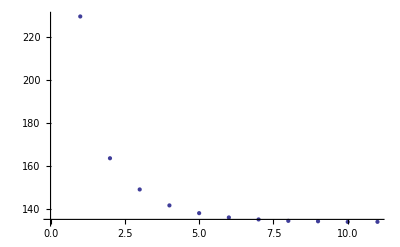

Ending w: {{{-0.246002,-0.102106,0.272222,-0.24708,-2.45146},{-1.06043,0.538195,1.78156,-0.278907,0.439735},{0.0755694,-1.93202,-0.774731,1.82264,-0.0435161},{-0.406073,0.0586717,-0.437144,-0.745172,-0.569067},{0.379373,0.41106,-0.625979,-0.175677,-1.73297}},{{-1.57595,-0.179858,-1.07281,0.373384,-0.66544,0.254464}}}

```mathematica
w=wold;scoretraj={};
(*Print["Starting w: ",w]*)
learn[trainingSet_,testSet_,niter_,wstart_]:=Module[{dwlist,trainingInput,trainingOutput,i,q,rate=eta,wnew=wstart},
(* iterate iter times *)
scoretraj={};
scoretraj=Append[scoretraj,score[wnew,trainingSet]];
For[i=1,i≤niter,i++,
(* randomly pick a training vector input and output pair *)
q=Random[Integer,{1,Length[trainingSet]}];
trainingInput = Map[Part[#,1]&,trainingSet];
trainingOutput = Map[Part[#,2]&,trainingSet];
dwlist=backPropagate2[trainingInput,trainingOutput,wnew];
wnew= wnew + rate* dwlist;
scoretraj=Append[scoretraj,score[wnew,trainingSet]];
];
wnew
]
learn[altTrainingSet,altTrainingSet,10,w];
ListPlot[scoretraj]
Print["Ending w: ",w];
```

### 13. Compare the training output to the neural network output

```mathematica
CellPrint[TextCell["Show the outputs for the training inputs vs the real outputs, and also for the test inputs.","Text",CellFrame->True,CellMargins->{{65,400},{10,10}}]]
```

Show the outputs for the training inputs vs the real outputs, and also for the test inputs.

```mathematica
checkPerformance[w_,trainingSet_]:=Module[{i,trainingInput,trainingOutput,nnOut,numberCorrect,numberWrong},
For[i=1,i≤Length[trainingSet],i++,
trainingInput = trainingSet[[i]][[1]];
trainingOutput=trainingSet[[i]][[2]];
nnOut=nnOutput[trainingSet[[i]][[1]],w][[1]];
bnnOut=If[nnOut>0.5,1,
If[nnOut<-0.5,-1,0]
];
Print["  ",i," output: ",trainingOutput," nn: ",nnOut," biased-nn: ",bnnOut];
If[bnnOut≠0,
If[trainingOutput==bnnOut,
numberCorrect++,numberWrong++],0
];
]
];
Print["Training Set"];
checkPerformance[w,altTrainingSet]
```

### 14. Finding the distribution of scores by training the neural network repeatedly

```mathematica
CellPrint[TextCell["The landscape for a neural network is most likely riddled with multiple minima, meaning that multiple runs from different initial conditions do not end up in the same solution space.  Therefore it is important to test whether the learning algorithm is robust.  One way to test is to perform multiple runs from different initial conditions, and examining the distribution of scores over all the training sessions.","Text",CellFrame->True,CellMargins->{{65,400},{10,10}}]]
```

The landscape for a neural network is most likely riddled with multiple minima, meaning that multiple runs from different initial conditions do not end up in the same solution space.  Therefore it is important to test whether the learning algorithm is robust.  One way to test is to perform multiple runs from different initial conditions, and examining the distribution of scores over all the training sessions.

```mathematica
scores={};
For[j=1,j≤100,j++,w={};
For[i=1,i≤(Length[stateSizeList]-1),i++,
q=RandomVariate[NormalDistribution[],{stateSizeList[[i+1]],stateSizeList[[i]]+1}];
w=Append[w,q];
];
w=learn[altTrainingSet,altTrainingSet,1000,w];
scores=Append[scores,score[w,altTrainingSet]];
]
```

```mathematica
CellPrint[TextCell["Here the training algorithm was run 100 times, each time with training length of 5000 steps.  Note that 80% of the runs ended with very low error, but 20% ended up rather high error.","Text",CellFrame->True,CellMargins->{{65,400},{10,10}}]]
```

Here the training algorithm was run 100 times, each time with training length of 5000 steps.  Note that 80% of the runs ended with very low error, but 20% ended up rather high error.

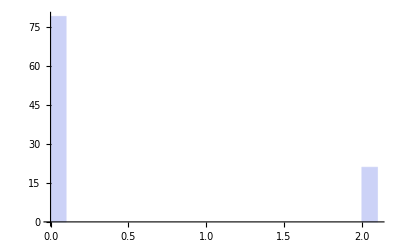

```mathematica
Histogram[scores,{0.1}]
```

```mathematica
CellPrint[TextCell["Running 100 times again but with a much shorter length of 1000 steps per training session leads to a distribution with many more high values, i.e. failed training sessions.","Text",CellFrame->True,CellMargins->{{65,400},{10,10}}]]
```

Running 100 times again but with a much shorter length of 1000 steps per training session leads to a distribution with many more high values, i.e. failed training sessions.  We might conclude that 5000 steps is necessary to train this kind of problem.

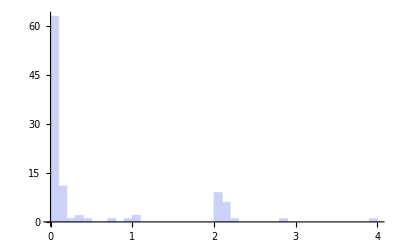

```mathematica
Histogram[scores,{0.1}]
```